# Evaluation

```mathematica
NotebookDirectory[]
```

/Users/jld/tmp/TSC/github/

```mathematica
dates=Import[NotebookDirectory[]<>"bytick/scores/basic/INTC.csv"][[61;;,1]];
```

How many of the top-ranked tickers do we select on a day we run the evaluation:

```mathematica
topK=10;
```

How many days do we track a stock’s performance after it's been picked:

```mathematica
window=20;
```

## Snapshot Absolute

```mathematica
AbsolutePricesSnapshot=Table[
tickers=StringDrop[Import[NotebookDirectory[]<>"/bydate/ranks/snapshot/"<>dates[[date]]<>".csv"][[1;;topK,2]],2];
files=Map[NotebookDirectory[]<>"Tickers/"<>#1<>"-hist.csv"&,tickers];
prices=Map[Import[#1][[{date+1,date+window},5]]&,files];
prices,{date,1,658}];
TickerPerfAtEndOfPeriodAbsoluteSnapshot=Map[1+(#[[2]]-#[[1]])/#[[1]]&,AbsolutePricesSnapshot,{2}];
RoiForEachEvaluateDateAbsoluteSnapshot=Apply[Plus,TickerPerfAtEndOfPeriodAbsoluteSnapshot,{1}]/topK;
CummulativePerfAbsoluteSnapshot=FoldList[#1*(1+(#2-1)/window)&,1,RoiForEachEvaluateDateAbsoluteSnapshot];
```

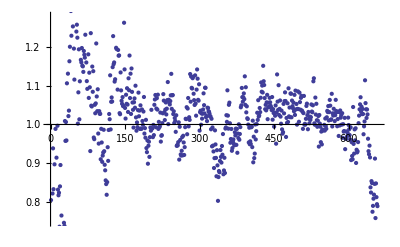

```mathematica
ListPlot[RoiForEachEvaluateDateAbsoluteSnapshot,AxesOrigin->{0,1}]
```

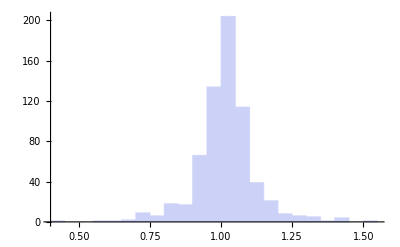

```mathematica
Histogram[RoiForEachEvaluateDateAbsoluteSnapshot]
```

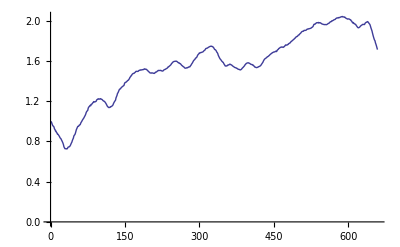

```mathematica
ListPlot[CummulativePerfAbsoluteSnapshot,Joined->True]
```

```mathematica
Mean[RoiForEachEvaluateDateAbsoluteSnapshot]
```

1.01665

```mathematica
CummulativePerfAbsoluteSnapshot[[-1]];
```

## Snapshot Aggregation

```mathematica
DeltaPricesSnapshot = Table[
tickers=StringDrop[Import[NotebookDirectory[]<>"/bydate/ranks/snapshot/"<>dates[[date]]<>".csv"][[1;;topK,2]],2];
files=Map[NotebookDirectory[]<>"bytick/stats/"<>#1<>".csv"&,tickers];
prices=Map[Import[#1][[date+1;;date+window,2]]&,files];
prices,{date,1,Length[dates]-window-2}];
TickerPerfAtEndOfPeriodDeltaSnapshot=Apply[Times,1+DeltaPricesSnapshot/100,{2}];
RoiForEachEvaluateDateDeltaSnapshot=Apply[Plus,TickerPerfAtEndOfPeriodDeltaSnapshot,{1}]/topK;CummulativePerfDeltaSnapshot=FoldList[#1*(1+(#2-1)/window)&,1,RoiForEachEvaluateDateDeltaSnapshot];
CumulativeGainDeltaSnapshot=CummulativePerfDeltaSnapshot[[-1]];
```

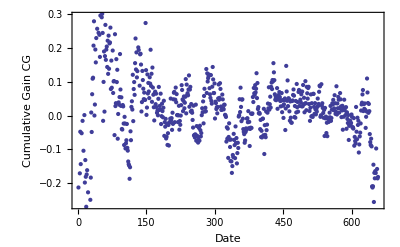

```mathematica
snapROI=ListPlot[RoiForEachEvaluateDateDeltaSnapshot-1,AxesOrigin->{0,0},Frame->True,FrameTicks->{Automatic,All},
FrameLabel->{"Date","Cumulative Gain CG"}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/Eval_Snapshot_ROI_K"<>ToString[topK]<>"_W"<>ToString[window]<>".pdf",snapROI]
```

/Users/jld/tmp/TSC/github/Figures/Eval_Snapshot_ROI_K10_W20.pdf

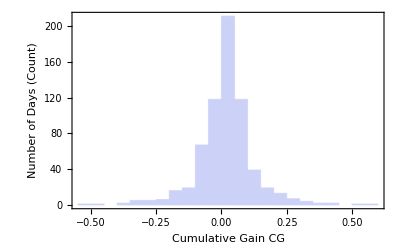

```mathematica
snapROIHisto=Histogram[RoiForEachEvaluateDateDeltaSnapshot-1,FrameTicks->{Automatic,All},Frame->True,
FrameLabel->{"Cumulative Gain CG","Number of Days (Count)"}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/Eval_Snapshot_ROIHisto_K"<>ToString[topK]<>"_W"<>ToString[window]<>".pdf",snapROIHisto]
```

/Users/jld/tmp/TSC/github/Figures/Eval_Snapshot_ROIHisto_K10_W20.pdf

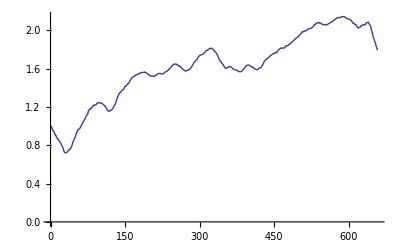

```mathematica
snapGain=ListPlot[CummulativePerfDeltaSnapshot,Joined->True]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/Eval_Snapshot_Gain_K"<>ToString[topK]<>"_W"<>ToString[window]<>".pdf",snapGain]
```

/Users/jld/tmp/TSC/github/Figures/Eval_Snapshot_Gain_K10_W20.pdf

```mathematica
yieldSAK10W20=GeometricMean[RoiForEachEvaluateDateDeltaSnapshot]
```

1.01194

## Histogram Aggregation

```mathematica
HistogramPrices = Table[
tickers=StringDrop[Import[NotebookDirectory[]<>"/bydate/ranks/histogram/"<>dates[[date]]<>".csv"][[1;;topK,2]],2];
files=Map[NotebookDirectory[]<>"bytick/stats/"<>#1<>".csv"&,tickers];
prices=Map[Import[#1][[date+1;;date+window,2]]&,files];
prices,{date,1,Length[dates]-window-2}];
HistogramTickerPerfAtEndOfPeriod=Apply[Times,1+HistogramPrices/100,{2}];
HistogramRoiForEachEvaluateDate=Apply[Plus,HistogramTickerPerfAtEndOfPeriod,{1}]/topK;HistogramCummulativePerf=FoldList[#1*(1+(#2-1)/window)&,1,HistogramRoiForEachEvaluateDate];
HistogramCumulativeGain=HistogramCummulativePerf[[-1]];
```

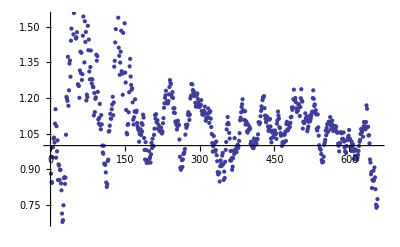

```mathematica
ListPlot[HistogramRoiForEachEvaluateDate,AxesOrigin->{0,1}]
```

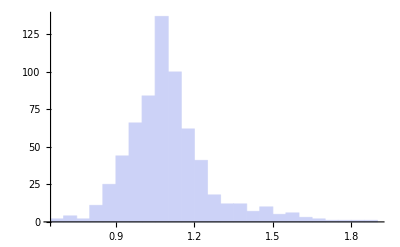

```mathematica
Histogram[HistogramRoiForEachEvaluateDate]
```

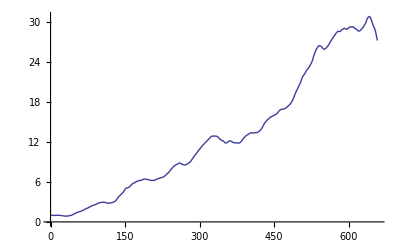

```mathematica
ListPlot[HistogramCummulativePerf,Joined->True]
```

```mathematica
yieldHAK10W20=GeometricMean[HistogramRoiForEachEvaluateDate]
```

1.09067

## Snapshot Skyline

```mathematica
SkylineSnapPrices = Table[
tickers=StringDrop[Import[NotebookDirectory[]<>"/bydate/ranks/skyline/snapshot/"<>dates[[date]]<>".csv"][[1;;topK,2]],2];
files=Map[NotebookDirectory[]<>"bytick/stats/"<>#1<>".csv"&,tickers];
prices=Map[Import[#1][[date+1;;date+window,2]]&,files];
prices,{date,1,Length[dates]-window-2}];
SkylineSnapTickerPerfAtEndOfPeriod=Apply[Times,1+SkylineSnapPrices/100,{2}];
SkylineSnapRoiForEachEvaluateDate=Apply[Plus,SkylineSnapTickerPerfAtEndOfPeriod,{1}]/topK;SkylineSnapCummulativePerf=FoldList[#1*(1+(#2-1)/window)&,1,SkylineSnapRoiForEachEvaluateDate];
SkylineSnapCumulativeGain=SkylineSnapCummulativePerf[[-1]];
```

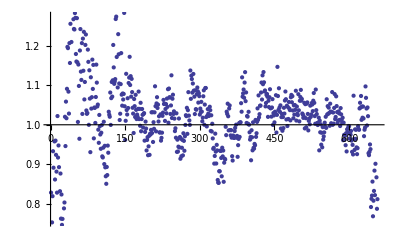

```mathematica
ListPlot[SkylineSnapRoiForEachEvaluateDate,AxesOrigin->{0,1}]
```

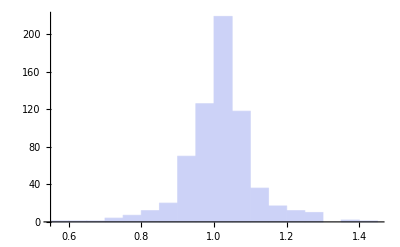

```mathematica
Histogram[SkylineSnapRoiForEachEvaluateDate]
```

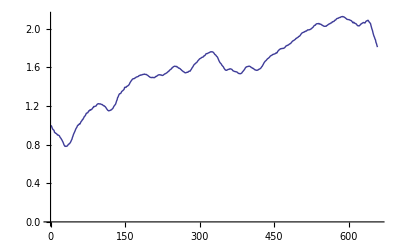

```mathematica
ListPlot[SkylineSnapCummulativePerf,Joined->True]
```

```mathematica
yieldSSK10W20=GeometricMean[SkylineSnapRoiForEachEvaluateDate]
```

1.0139

## Histogram Skyline

```mathematica
SkylineHistoPrices = Table[
tickers=StringDrop[Import[NotebookDirectory[]<>"/bydate/ranks/skyline/histogram/"<>dates[[date]]<>".csv"][[1;;topK,2]],2];
files=Map[NotebookDirectory[]<>"bytick/stats/"<>#1<>".csv"&,tickers];
prices=Map[Import[#1][[date+1;;date+window,2]]&,files];
prices,{date,1,Length[dates]-window-2}];
SkylineHistoTickerPerfAtEndOfPeriod=Apply[Times,1+SkylineHistoPrices/100,{2}];
SkylineHistoRoiForEachEvaluateDate=Apply[Plus,SkylineHistoTickerPerfAtEndOfPeriod,{1}]/topK;SkylineHistoCummulativePerf=FoldList[#1*(1+(#2-1)/window)&,1,SkylineHistoRoiForEachEvaluateDate];
SkylineHistoCumulativeGain=SkylineHistoCummulativePerf[[-1]];
```

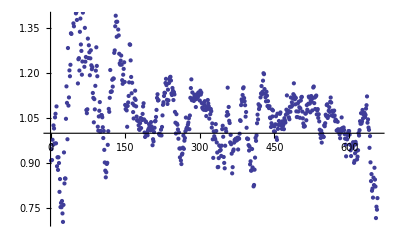

```mathematica
ListPlot[SkylineHistoRoiForEachEvaluateDate,AxesOrigin->{0,1}]
```

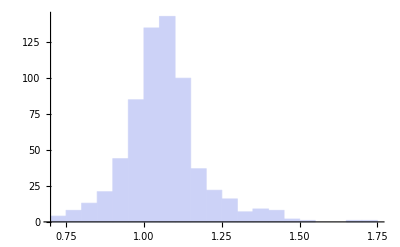

```mathematica
Histogram[SkylineHistoRoiForEachEvaluateDate]
```

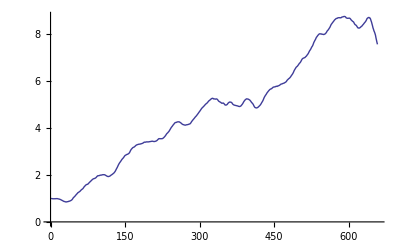

```mathematica
ListPlot[SkylineHistoCummulativePerf,Joined->True]
```

```mathematica
yieldHSK10W20=GeometricMean[SkylineHistoRoiForEachEvaluateDate]
```

1.05506

## Comparison

```mathematica
makePlotLegend[names_,markers_,origin_,markerSize_,fontSize_,font_]:=Join@@Table[{Text[Style[names[[i]],FontSize->fontSize,font],Offset[{1.5*markerSize,-(i-0.5)*Max[markerSize,fontSize]*1.25},Scaled[origin]],{-1,0}],Inset[Show[markers[[i]],ImageSize->markerSize],Offset[{markerSize/2,-(i-0.5)*Max[markerSize,fontSize]*1.25},Scaled[origin]],{0,0},Background->Directive[Opacity[0],White]]},{i,1,Length[names]}];
```

```mathematica
AlgoColors={RGBColor[.44,.56,.52],RGBColor[.36,.34,.37],RGBColor[.73,.54,.44],RGBColor[.83,.77,.45]}
```

{RGBColor[0.44,0.56,0.52],RGBColor[0.36,0.34,0.37],RGBColor[0.73,0.54,0.44],RGBColor[0.83,0.77,0.45]}

```mathematica
plotGain1=ListPlot[{HistogramCummulativePerf,SkylineHistoCummulativePerf,CummulativePerfDeltaSnapshot,SkylineSnapCummulativePerf}, Joined->True,PlotMarkers->None,FrameTicks->{Automatic,All},
FrameLabel->{"Date","Overall Gain"},PlotStyle->Thread[Directive[AlgoColors,Thick]],Frame->True,PlotRange->All,Epilog->makePlotLegend[{"Dynamis Aggregation","Dynamis Skyline","Snapshot Aggregation","Snapshot Skyline"},(Graphics[{Thickness[1],#,Line[{{-1,0},{1,0}}]}])&/@AlgoColors,{0.2,0.95},12,12,"Arial"]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/Eval_Compare_K"<>ToString[topK]<>"_W"<>ToString[window]<>".pdf",plotGain1]
```

/Users/jld/tmp/TSC/github/Figures/Eval_Compare_K10_W20.pdf

```mathematica
plotGain2=ListPlot[{CummulativePerfDeltaSnapshot,SkylineSnapCummulativePerf}, Joined->True,PlotMarkers->None,FrameTicks->{Automatic,All},
FrameLabel->{"Date","Overall Gain"},PlotStyle->AlgoColors[[3;;4]],Frame->True,Epilog->makePlotLegend[{"Snapshot Aggregation","Snapshot Skyline"},(Graphics[{Thickness[1],#,Line[{{-1,0},{1,0}}]}])&/@AlgoColors[[3;;4]],{0.3,0.25},12,12,"Arial"]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/Eval_Compare_Snapshot_K"<>ToString[topK]<>"_W"<>ToString[window]<>".pdf",plotGain2]
```

/Users/jld/tmp/TSC/github/Figures/Eval_Compare_Snapshot_K10_W20.pdf

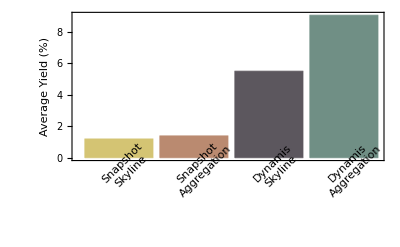

```mathematica
geomean=BarChart[100*{yieldSAK10W20-1,yieldSSK10W20-1,yieldHSK10W20-1,yieldHAK10W20-1},
ChartLabels->Placed[{"Snapshot\nSkyline","Snapshot\nAggregation","Dynamis\nSkyline","Dynamis\nAggregation"},Axis,Rotate[#,45Degree]&],ChartStyle->Reverse[AlgoColors],FrameLabel->{None,"Average Yield (%)"},
FrameTicks->{None,Automatic},Frame->True]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/Eval_Compare_GeoMean_K"<>ToString[topK]<>"_W"<>ToString[window]<>".pdf",geomean]
```

/Users/jld/tmp/TSC/github/Figures/Eval_Compare_GeoMean_K10_W20.pdf

Dump the internal of these computations so it can be reloaded (with Get[“EvalState.mx”] )...

```mathematica
DumpSave[NotebookDirectory[]<>"EvalState_K"<>ToString[topK]<>"_W"<>ToString[window]<>".mx","Global`"]
```

{Global`}

```mathematica
NotebookSave[EvaluationNotebook[]]
```